A simple substitution rule example, over a two letters alphabet (“0” and “1”).

```mathematica
lapin[l_]:=Flatten[Replace[#,{1->{1,0},0->{1}}]&/@l]
```

We see that the legal see “0” makes the iterate lapin^n converge for the discrete product topology, in the sense that
lim_(n→∞) lapin^n(0) =w, such that lapin(w) = w.
An indication of convergence is the fact that the word does not vary too much after some iterations, as examplified by the ArrayPlot below.

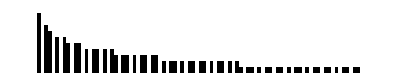

```mathematica
NestList[lapin,{0},10]//ArrayPlot
```

Actually,
w^(i+2) = w^(i+1)w^(i)